```mathematica
$PlotTheme="Scientific"
```

Scientific

```mathematica
SetOptions[{Plot,ListPlot,ArrayPlot,ContourPlot,DiscretePlot3D},BaseStyle->{14,Directive[FontFamily->"cmr10"]}];
```

# All intertwiners Immirzi 0.1

## Load the Data

```mathematica
SetDirectory[NotebookDirectory[]]
```

/home/pdona/Dropbox/Ongoing Projects/OtherEPRLDivergences/Spinfoam_radiative_corrections/Notebooks

```mathematica
DATA = "../data/EPRL/immirzi_0.1/propagator_matrix/bspin_0.5/cutoff_10.0/Dl_0/frogface_pcutoff_0.0.csv";
```

```mathematica
getfile[Dl_,K_]:=  StringJoin["../CLUSTER_COMPUTATIONS/data/EPRL/immirzi_0.1/propagator_matrix/bspin_0.5/cutoff_10.0/Dl_",ToString[Dl],"/frogface_pcutoff_",ToString[NumberForm[N[K],{3,1}]],".csv"];
```

```mathematica
getfile[0,1/2]
```

../CLUSTER_COMPUTATIONS/data/EPRL/immirzi_0.1/propagator_matrix/bspin_0.5/cutoff_10.0/Dl_0/frogface_pcutoff_0.5.csv

```mathematica
NumberForm[N[2],{3,1}]
```

2.0

```mathematica
A00KDl0 = {};
A01KDl0 = {};
A11KDl0 = {};
For[k=0, k ≤10, k+=1/2,
{{tmp00,tmp01},{tmp10,tmp11}}=Transpose@Import[getfile[0,k],"Data",HeaderLines->1];
AppendTo[A00KDl0,{k,tmp00}];
AppendTo[A01KDl0,{k,tmp01}];
AppendTo[A11KDl0,{k,tmp11}];
]
```

Import::nffil: File ../CLUSTER_COMPUTATIONS/data/EPRL/immirzi_0.1/propagator_matrix/bspin_0.5/cutoff_10.0/Dl_0/frogface_pcutoff_0.0.csv not found during Import.

Set::shape: Lists {{tmp00,tmp01},{tmp10,tmp11}} and Transpose[$Failed] are not the same shape.

Import::nffil: File ../CLUSTER_COMPUTATIONS/data/EPRL/immirzi_0.1/propagator_matrix/bspin_0.5/cutoff_10.0/Dl_0/frogface_pcutoff_0.5.csv not found during Import.

Set::shape: Lists {{tmp00,tmp01},{tmp10,tmp11}} and Transpose[$Failed] are not the same shape.

Import::nffil: File ../CLUSTER_COMPUTATIONS/data/EPRL/immirzi_0.1/propagator_matrix/bspin_0.5/cutoff_10.0/Dl_0/frogface_pcutoff_1.0.csv not found during Import.

General::stop: Further output of Import::nffil will be suppressed during this calculation.

Set::shape: Lists {{tmp00,tmp01},{tmp10,tmp11}} and Transpose[$Failed] are not the same shape.

General::stop: Further output of Set::shape will be suppressed during this calculation.

```mathematica
A00KDl1 = {};
A01KDl1 = {};
A11KDl1 = {};
For[k=0, k ≤10, k+=1/2,
{{tmp00,tmp01},{tmp10,tmp11}}=Transpose@Import[getfile[1,k],"Data",HeaderLines->1];
AppendTo[A00KDl1,{k,tmp00}];
AppendTo[A01KDl1,{k,tmp01}];
AppendTo[A11KDl1,{k,tmp11}];
]
```

Import::nffil: File ../CLUSTER_COMPUTATIONS/data/EPRL/immirzi_0.1/propagator_matrix/bspin_0.5/cutoff_10.0/Dl_1/frogface_pcutoff_0.0.csv not found during Import.

Set::shape: Lists {{tmp00,tmp01},{tmp10,tmp11}} and Transpose[$Failed] are not the same shape.

Import::nffil: File ../CLUSTER_COMPUTATIONS/data/EPRL/immirzi_0.1/propagator_matrix/bspin_0.5/cutoff_10.0/Dl_1/frogface_pcutoff_0.5.csv not found during Import.

Set::shape: Lists {{tmp00,tmp01},{tmp10,tmp11}} and Transpose[$Failed] are not the same shape.

Import::nffil: File ../CLUSTER_COMPUTATIONS/data/EPRL/immirzi_0.1/propagator_matrix/bspin_0.5/cutoff_10.0/Dl_1/frogface_pcutoff_1.0.csv not found during Import.

General::stop: Further output of Import::nffil will be suppressed during this calculation.

Set::shape: Lists {{tmp00,tmp01},{tmp10,tmp11}} and Transpose[$Failed] are not the same shape.

General::stop: Further output of Set::shape will be suppressed during this calculation.

```mathematica
A00KDl2 = {};
A01KDl2 = {};
A11KDl2 = {};
For[k=0, k ≤10, k+=1/2,
{{tmp00,tmp01},{tmp10,tmp11}}=Transpose@Import[getfile[2,k],"Data",HeaderLines->1];
AppendTo[A00KDl2,{k,tmp00}];
AppendTo[A01KDl2,{k,tmp01}];
AppendTo[A11KDl2,{k,tmp11}];
]
```

Import::nffil: File ../CLUSTER_COMPUTATIONS/data/EPRL/immirzi_0.1/propagator_matrix/bspin_0.5/cutoff_10.0/Dl_2/frogface_pcutoff_0.0.csv not found during Import.

Set::shape: Lists {{tmp00,tmp01},{tmp10,tmp11}} and Transpose[$Failed] are not the same shape.

Import::nffil: File ../CLUSTER_COMPUTATIONS/data/EPRL/immirzi_0.1/propagator_matrix/bspin_0.5/cutoff_10.0/Dl_2/frogface_pcutoff_0.5.csv not found during Import.

Set::shape: Lists {{tmp00,tmp01},{tmp10,tmp11}} and Transpose[$Failed] are not the same shape.

Import::nffil: File ../CLUSTER_COMPUTATIONS/data/EPRL/immirzi_0.1/propagator_matrix/bspin_0.5/cutoff_10.0/Dl_2/frogface_pcutoff_1.0.csv not found during Import.

General::stop: Further output of Import::nffil will be suppressed during this calculation.

Set::shape: Lists {{tmp00,tmp01},{tmp10,tmp11}} and Transpose[$Failed] are not the same shape.

General::stop: Further output of Set::shape will be suppressed during this calculation.

```mathematica
A00KDl3 = {};
A01KDl3 = {};
A11KDl3 = {};
For[k=0, k ≤10, k+=1/2,
{{tmp00,tmp01},{tmp10,tmp11}}=Transpose@Import[getfile[3,k],"Data",HeaderLines->1];
AppendTo[A00KDl3,{k,tmp00}];
AppendTo[A01KDl3,{k,tmp01}];
AppendTo[A11KDl3,{k,tmp11}];
]
```

Import::nffil: File ../CLUSTER_COMPUTATIONS/data/EPRL/immirzi_0.1/propagator_matrix/bspin_0.5/cutoff_10.0/Dl_3/frogface_pcutoff_0.0.csv not found during Import.

Set::shape: Lists {{tmp00,tmp01},{tmp10,tmp11}} and Transpose[$Failed] are not the same shape.

Import::nffil: File ../CLUSTER_COMPUTATIONS/data/EPRL/immirzi_0.1/propagator_matrix/bspin_0.5/cutoff_10.0/Dl_3/frogface_pcutoff_0.5.csv not found during Import.

Set::shape: Lists {{tmp00,tmp01},{tmp10,tmp11}} and Transpose[$Failed] are not the same shape.

Import::nffil: File ../CLUSTER_COMPUTATIONS/data/EPRL/immirzi_0.1/propagator_matrix/bspin_0.5/cutoff_10.0/Dl_3/frogface_pcutoff_1.0.csv not found during Import.

General::stop: Further output of Import::nffil will be suppressed during this calculation.

Set::shape: Lists {{tmp00,tmp01},{tmp10,tmp11}} and Transpose[$Failed] are not the same shape.

General::stop: Further output of Set::shape will be suppressed during this calculation.

```mathematica
A00KDl4 = {};
A01KDl4 = {};
A11KDl4 = {};
For[k=0, k ≤10, k+=1/2,
{{tmp00,tmp01},{tmp10,tmp11}}=Transpose@Import[getfile[4,k],"Data",HeaderLines->1];
AppendTo[A00KDl4,{k,tmp00}];
AppendTo[A01KDl4,{k,tmp01}];
AppendTo[A11KDl4,{k,tmp11}];
]
```

Import::nffil: File ../CLUSTER_COMPUTATIONS/data/EPRL/immirzi_0.1/propagator_matrix/bspin_0.5/cutoff_10.0/Dl_4/frogface_pcutoff_0.0.csv not found during Import.

Set::shape: Lists {{tmp00,tmp01},{tmp10,tmp11}} and Transpose[$Failed] are not the same shape.

Import::nffil: File ../CLUSTER_COMPUTATIONS/data/EPRL/immirzi_0.1/propagator_matrix/bspin_0.5/cutoff_10.0/Dl_4/frogface_pcutoff_0.5.csv not found during Import.

Set::shape: Lists {{tmp00,tmp01},{tmp10,tmp11}} and Transpose[$Failed] are not the same shape.

Import::nffil: File ../CLUSTER_COMPUTATIONS/data/EPRL/immirzi_0.1/propagator_matrix/bspin_0.5/cutoff_10.0/Dl_4/frogface_pcutoff_1.0.csv not found during Import.

General::stop: Further output of Import::nffil will be suppressed during this calculation.

Set::shape: Lists {{tmp00,tmp01},{tmp10,tmp11}} and Transpose[$Failed] are not the same shape.

General::stop: Further output of Set::shape will be suppressed during this calculation.

```mathematica
A00KDl5 = {};
A01KDl5 = {};
A11KDl5 = {};
For[k=0, k ≤10, k+=1/2,
{{tmp00,tmp01},{tmp10,tmp11}}=Transpose@Import[getfile[5,k],"Data",HeaderLines->1];
AppendTo[A00KDl5,{k,tmp00}];
AppendTo[A01KDl5,{k,tmp01}];
AppendTo[A11KDl5,{k,tmp11}];
]
```

Import::nffil: File ../CLUSTER_COMPUTATIONS/data/EPRL/immirzi_0.1/propagator_matrix/bspin_0.5/cutoff_10.0/Dl_5/frogface_pcutoff_0.0.csv not found during Import.

Set::shape: Lists {{tmp00,tmp01},{tmp10,tmp11}} and Transpose[$Failed] are not the same shape.

Import::nffil: File ../CLUSTER_COMPUTATIONS/data/EPRL/immirzi_0.1/propagator_matrix/bspin_0.5/cutoff_10.0/Dl_5/frogface_pcutoff_0.5.csv not found during Import.

Set::shape: Lists {{tmp00,tmp01},{tmp10,tmp11}} and Transpose[$Failed] are not the same shape.

Import::nffil: File ../CLUSTER_COMPUTATIONS/data/EPRL/immirzi_0.1/propagator_matrix/bspin_0.5/cutoff_10.0/Dl_5/frogface_pcutoff_1.0.csv not found during Import.

General::stop: Further output of Import::nffil will be suppressed during this calculation.

Set::shape: Lists {{tmp00,tmp01},{tmp10,tmp11}} and Transpose[$Failed] are not the same shape.

General::stop: Further output of Set::shape will be suppressed during this calculation.

```mathematica
A00KDl6 = {};
A01KDl6 = {};
A11KDl6 = {};
For[k=0, k ≤10, k+=1/2,
{{tmp00,tmp01},{tmp10,tmp11}}=Transpose@Import[getfile[6,k],"Data",HeaderLines->1];
AppendTo[A00KDl6,{k,tmp00}];
AppendTo[A01KDl6,{k,tmp01}];
AppendTo[A11KDl6,{k,tmp11}];
]
```

Import::nffil: File ../CLUSTER_COMPUTATIONS/data/EPRL/immirzi_0.1/propagator_matrix/bspin_0.5/cutoff_10.0/Dl_6/frogface_pcutoff_0.0.csv not found during Import.

Set::shape: Lists {{tmp00,tmp01},{tmp10,tmp11}} and Transpose[$Failed] are not the same shape.

Import::nffil: File ../CLUSTER_COMPUTATIONS/data/EPRL/immirzi_0.1/propagator_matrix/bspin_0.5/cutoff_10.0/Dl_6/frogface_pcutoff_0.5.csv not found during Import.

Set::shape: Lists {{tmp00,tmp01},{tmp10,tmp11}} and Transpose[$Failed] are not the same shape.

Import::nffil: File ../CLUSTER_COMPUTATIONS/data/EPRL/immirzi_0.1/propagator_matrix/bspin_0.5/cutoff_10.0/Dl_6/frogface_pcutoff_1.0.csv not found during Import.

General::stop: Further output of Import::nffil will be suppressed during this calculation.

Set::shape: Lists {{tmp00,tmp01},{tmp10,tmp11}} and Transpose[$Failed] are not the same shape.

General::stop: Further output of Set::shape will be suppressed during this calculation.

```mathematica
A00KDl7 = {};
A01KDl7 = {};
A11KDl7 = {};
For[k=0, k ≤10, k+=1/2,
{{tmp00,tmp01},{tmp10,tmp11}}=Transpose@Import[getfile[7,k],"Data",HeaderLines->1];
AppendTo[A00KDl7,{k,tmp00}];
AppendTo[A01KDl7,{k,tmp01}];
AppendTo[A11KDl7,{k,tmp11}];
]
```

Import::nffil: File ../CLUSTER_COMPUTATIONS/data/EPRL/immirzi_0.1/propagator_matrix/bspin_0.5/cutoff_10.0/Dl_7/frogface_pcutoff_0.0.csv not found during Import.

Set::shape: Lists {{tmp00,tmp01},{tmp10,tmp11}} and Transpose[$Failed] are not the same shape.

Import::nffil: File ../CLUSTER_COMPUTATIONS/data/EPRL/immirzi_0.1/propagator_matrix/bspin_0.5/cutoff_10.0/Dl_7/frogface_pcutoff_0.5.csv not found during Import.

Set::shape: Lists {{tmp00,tmp01},{tmp10,tmp11}} and Transpose[$Failed] are not the same shape.

Import::nffil: File ../CLUSTER_COMPUTATIONS/data/EPRL/immirzi_0.1/propagator_matrix/bspin_0.5/cutoff_10.0/Dl_7/frogface_pcutoff_1.0.csv not found during Import.

General::stop: Further output of Import::nffil will be suppressed during this calculation.

Set::shape: Lists {{tmp00,tmp01},{tmp10,tmp11}} and Transpose[$Failed] are not the same shape.

General::stop: Further output of Set::shape will be suppressed during this calculation.

```mathematica
A00KDl8 = {};
A01KDl8 = {};
A11KDl8 = {};
For[k=0, k ≤10, k+=1/2,
{{tmp00,tmp01},{tmp10,tmp11}}=Transpose@Import[getfile[8,k],"Data",HeaderLines->1];
AppendTo[A00KDl8,{k,tmp00}];
AppendTo[A01KDl8,{k,tmp01}];
AppendTo[A11KDl8,{k,tmp11}];
]
```

Import::nffil: File ../CLUSTER_COMPUTATIONS/data/EPRL/immirzi_0.1/propagator_matrix/bspin_0.5/cutoff_10.0/Dl_8/frogface_pcutoff_0.0.csv not found during Import.

Set::shape: Lists {{tmp00,tmp01},{tmp10,tmp11}} and Transpose[$Failed] are not the same shape.

Import::nffil: File ../CLUSTER_COMPUTATIONS/data/EPRL/immirzi_0.1/propagator_matrix/bspin_0.5/cutoff_10.0/Dl_8/frogface_pcutoff_0.5.csv not found during Import.

Set::shape: Lists {{tmp00,tmp01},{tmp10,tmp11}} and Transpose[$Failed] are not the same shape.

Import::nffil: File ../CLUSTER_COMPUTATIONS/data/EPRL/immirzi_0.1/propagator_matrix/bspin_0.5/cutoff_10.0/Dl_8/frogface_pcutoff_1.0.csv not found during Import.

General::stop: Further output of Import::nffil will be suppressed during this calculation.

Set::shape: Lists {{tmp00,tmp01},{tmp10,tmp11}} and Transpose[$Failed] are not the same shape.

General::stop: Further output of Set::shape will be suppressed during this calculation.

```mathematica
A00KDl9 = {};
A01KDl9 = {};
A11KDl9 = {};
For[k=0, k ≤10, k+=1/2,
{{tmp00,tmp01},{tmp10,tmp11}}=Transpose@Import[getfile[9,k],"Data",HeaderLines->1];
AppendTo[A00KDl9,{k,tmp00}];
AppendTo[A01KDl9,{k,tmp01}];
AppendTo[A11KDl9,{k,tmp11}];
]
```

Import::nffil: File ../CLUSTER_COMPUTATIONS/data/EPRL/immirzi_0.1/propagator_matrix/bspin_0.5/cutoff_10.0/Dl_9/frogface_pcutoff_0.0.csv not found during Import.

Set::shape: Lists {{tmp00,tmp01},{tmp10,tmp11}} and Transpose[$Failed] are not the same shape.

Import::nffil: File ../CLUSTER_COMPUTATIONS/data/EPRL/immirzi_0.1/propagator_matrix/bspin_0.5/cutoff_10.0/Dl_9/frogface_pcutoff_0.5.csv not found during Import.

Set::shape: Lists {{tmp00,tmp01},{tmp10,tmp11}} and Transpose[$Failed] are not the same shape.

Import::nffil: File ../CLUSTER_COMPUTATIONS/data/EPRL/immirzi_0.1/propagator_matrix/bspin_0.5/cutoff_10.0/Dl_9/frogface_pcutoff_1.0.csv not found during Import.

General::stop: Further output of Import::nffil will be suppressed during this calculation.

Set::shape: Lists {{tmp00,tmp01},{tmp10,tmp11}} and Transpose[$Failed] are not the same shape.

General::stop: Further output of Set::shape will be suppressed during this calculation.

```mathematica
A00KDl10 = {};
A01KDl10 = {};
A11KDl10 = {};
For[k=0, k ≤10, k+=1/2,
{{tmp00,tmp01},{tmp10,tmp11}}=Transpose@Import[getfile[10,k],"Data",HeaderLines->1];
AppendTo[A00KDl10,{k,tmp00}];
AppendTo[A01KDl10,{k,tmp01}];
AppendTo[A11KDl10,{k,tmp11}];
]
```

Import::nffil: File ../CLUSTER_COMPUTATIONS/data/EPRL/immirzi_0.1/propagator_matrix/bspin_0.5/cutoff_10.0/Dl_10/frogface_pcutoff_0.0.csv not found during Import.

Set::shape: Lists {{tmp00,tmp01},{tmp10,tmp11}} and Transpose[$Failed] are not the same shape.

Import::nffil: File ../CLUSTER_COMPUTATIONS/data/EPRL/immirzi_0.1/propagator_matrix/bspin_0.5/cutoff_10.0/Dl_10/frogface_pcutoff_0.5.csv not found during Import.

Set::shape: Lists {{tmp00,tmp01},{tmp10,tmp11}} and Transpose[$Failed] are not the same shape.

Import::nffil: File ../CLUSTER_COMPUTATIONS/data/EPRL/immirzi_0.1/propagator_matrix/bspin_0.5/cutoff_10.0/Dl_10/frogface_pcutoff_1.0.csv not found during Import.

General::stop: Further output of Import::nffil will be suppressed during this calculation.

Set::shape: Lists {{tmp00,tmp01},{tmp10,tmp11}} and Transpose[$Failed] are not the same shape.

General::stop: Further output of Set::shape will be suppressed during this calculation.

```mathematica
Clear[k]
```

## Extrapolation using Series convergence acceleration

```mathematica
Aitken[AD_]:=(AD[[-1]]AD[[-3]]-AD[[-2]]^2)/(AD[[-1]]-2AD[[-2]]+AD[[-3]])
```

```mathematica
rExtrapolation00= Aitken/@Transpose[{Last/@A00KDl0,Last/@A00KDl1,Last/@A00KDl2,Last/@A00KDl3,Last/@A00KDl4,Last/@A00KDl5,Last/@A00KDl6,Last/@A00KDl7,Last/@A00KDl8,Last/@A00KDl9,Last/@A00KDl10}]
rExtrapolation01=Aitken/@Transpose[{Last/@A01KDl0,Last/@A01KDl1,Last/@A01KDl2,Last/@A01KDl3,Last/@A01KDl4,Last/@A01KDl5,Last/@A01KDl6,Last/@A01KDl7,Last/@A01KDl8,Last/@A01KDl9,Last/@A01KDl10}]
rExtrapolation11=Aitken/@Transpose[{Last/@A11KDl0,Last/@A11KDl1,Last/@A11KDl2,Last/@A11KDl3,Last/@A11KDl4,Last/@A11KDl5,Last/@A11KDl6,Last/@A11KDl7,Last/@A11KDl8,Last/@A11KDl9,Last/@A11KDl10}]
```

Power::infy: Infinite expression 1/0 encountered.

Infinity::indet: Indeterminate expression 0 ComplexInfinity encountered.

Power::infy: Infinite expression 1/0 encountered.

Infinity::indet: Indeterminate expression 0 ComplexInfinity encountered.

Power::infy: Infinite expression 1/0 encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression 0 ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

{Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate}

Power::infy: Infinite expression 1/0 encountered.

Infinity::indet: Indeterminate expression 0 ComplexInfinity encountered.

Power::infy: Infinite expression 1/0 encountered.

Infinity::indet: Indeterminate expression 0 ComplexInfinity encountered.

Power::infy: Infinite expression 1/0 encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression 0 ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

{Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate}

Power::infy: Infinite expression 1/0 encountered.

Infinity::indet: Indeterminate expression 0 ComplexInfinity encountered.

Power::infy: Infinite expression 1/0 encountered.

Infinity::indet: Indeterminate expression 0 ComplexInfinity encountered.

Power::infy: Infinite expression 1/0 encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression 0 ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

{Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate}

```mathematica
Extrapolation00=Join[{{0,0}},Table[{k,#[[2k+1]]},{k,1/2,10,1/2}]&@rExtrapolation00];
Extrapolation01=Join[{{0,0}},Table[{k,#[[2k+1]]},{k,1/2,10,1/2}]&@rExtrapolation01];
Extrapolation11=Join[{{0,0}},Table[{k,#[[2k+1]]},{k,1/2,10,1/2}]&@rExtrapolation11];
```

### Intertwiners 00

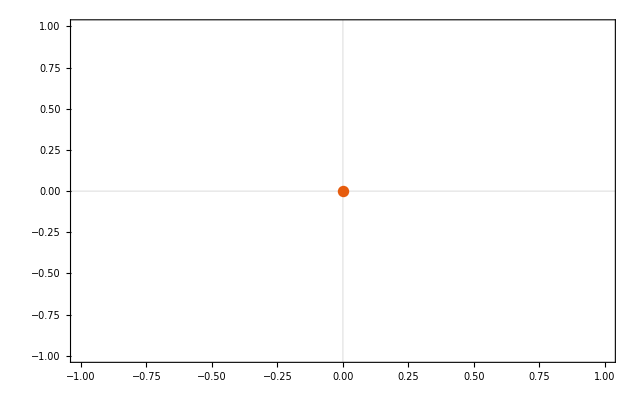

```mathematica
ListPlot[{Extrapolation00}]
```

```mathematica
fitExtrap00=NonlinearModelFit[Extrapolation00[[5;;]], a Log[k] +b + c/k +d/k^2 ,{a,b,c,d},k]
```

FindFit::fitm: Unable to solve for the fit parameters; the design matrix is nonrectangular, non-numerical, or could not be inverted.

NonlinearModelFit[{{2,Indeterminate},{5/2,Indeterminate},{3,Indeterminate},{7/2,Indeterminate},{4,Indeterminate},{9/2,Indeterminate},{5,Indeterminate},{11/2,Indeterminate},{6,Indeterminate},{13/2,Indeterminate},{7,Indeterminate},{15/2,Indeterminate},{8,Indeterminate},{17/2,Indeterminate},{9,Indeterminate},{19/2,Indeterminate},{10,Indeterminate}},b+d/k^2+c/k+a Log[k],{a,b,c,d},k]

```mathematica
fitExtrap00=NonlinearModelFit[Extrapolation00[[5;;]], b + c/k +d/k^2 ,{b,c,d},k]
```

FindFit::fitm: Unable to solve for the fit parameters; the design matrix is nonrectangular, non-numerical, or could not be inverted.

NonlinearModelFit[{{2,Indeterminate},{5/2,Indeterminate},{3,Indeterminate},{7/2,Indeterminate},{4,Indeterminate},{9/2,Indeterminate},{5,Indeterminate},{11/2,Indeterminate},{6,Indeterminate},{13/2,Indeterminate},{7,Indeterminate},{15/2,Indeterminate},{8,Indeterminate},{17/2,Indeterminate},{9,Indeterminate},{19/2,Indeterminate},{10,Indeterminate}},b+d/k^2+c/k,{b,c,d},k]

```mathematica
fitExtrap00["ParameterConfidenceIntervals"]
```

FindFit::fitm: Unable to solve for the fit parameters; the design matrix is nonrectangular, non-numerical, or could not be inverted.

NonlinearModelFit[{{2,Indeterminate},{5/2,Indeterminate},{3,Indeterminate},{7/2,Indeterminate},{4,Indeterminate},{9/2,Indeterminate},{5,Indeterminate},{11/2,Indeterminate},{6,Indeterminate},{13/2,Indeterminate},{7,Indeterminate},{15/2,Indeterminate},{8,Indeterminate},{17/2,Indeterminate},{9,Indeterminate},{19/2,Indeterminate},{10,Indeterminate}},b+d/k^2+c/k,{b,c,d},k][ParameterConfidenceIntervals]

```mathematica
fit1 =First/@fitExtrap00["ParameterConfidenceIntervals"].{1,1/k , 1/k^2};
fit2 =Last/@fitExtrap00["ParameterConfidenceIntervals"].{1,1/k , 1/k^2};
```

FindFit::fitm: Unable to solve for the fit parameters; the design matrix is nonrectangular, non-numerical, or could not be inverted.

First::normal: Nonatomic expression expected at position 1 in First[ParameterConfidenceIntervals].

FindFit::fitm: Unable to solve for the fit parameters; the design matrix is nonrectangular, non-numerical, or could not be inverted.

General::stop: Further output of FindFit::fitm will be suppressed during this calculation.

FindFit::fitm: Unable to solve for the fit parameters; the design matrix is nonrectangular, non-numerical, or could not be inverted.

Last::normal: Nonatomic expression expected at position 1 in Last[ParameterConfidenceIntervals].

FindFit::fitm: Unable to solve for the fit parameters; the design matrix is nonrectangular, non-numerical, or could not be inverted.

General::stop: Further output of FindFit::fitm will be suppressed during this calculation.

General::ivar: 1.00019 is not a valid variable.

General::stop: Further output of General::ivar will be suppressed during this calculation.

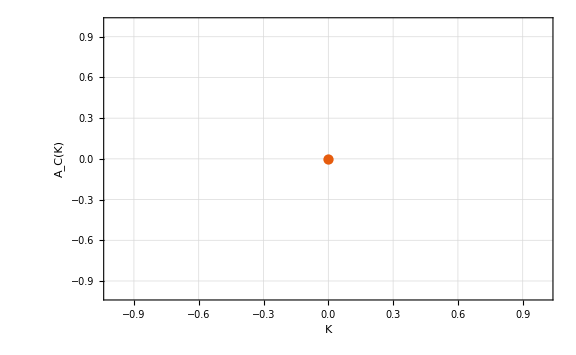

```mathematica
Show[Plot[{fit1,fit2},{k,1,10.5},PlotStyle->Blue,Filling->{1->{2}},GridLines->Automatic,FrameLabel->{"K","A_C(K)"},ImageSize->Large],ListPlot[Extrapolation00,PlotRange->All],PlotRange->All]
```

### Intertwiners 11

```mathematica
ListPlot[{Extrapolation11}]
```

-Graphics-

```mathematica
fitExtrap11=NonlinearModelFit[Extrapolation11[[5;;]], a Log[k] +b + c/k +d/k^2 ,{a,b,c,d},k]
```

FindFit::fitm: Unable to solve for the fit parameters; the design matrix is nonrectangular, non-numerical, or could not be inverted.

NonlinearModelFit[{{2,Indeterminate},{5/2,Indeterminate},{3,Indeterminate},{7/2,Indeterminate},{4,Indeterminate},{9/2,Indeterminate},{5,Indeterminate},{11/2,Indeterminate},{6,Indeterminate},{13/2,Indeterminate},{7,Indeterminate},{15/2,Indeterminate},{8,Indeterminate},{17/2,Indeterminate},{9,Indeterminate},{19/2,Indeterminate},{10,Indeterminate}},b+d/k^2+c/k+a Log[k],{a,b,c,d},k]

```mathematica
fitExtrap11=NonlinearModelFit[Extrapolation11[[5;;]], b + c/k +d/k^2 ,{b,c,d},k]
```

FindFit::fitm: Unable to solve for the fit parameters; the design matrix is nonrectangular, non-numerical, or could not be inverted.

NonlinearModelFit[{{2,Indeterminate},{5/2,Indeterminate},{3,Indeterminate},{7/2,Indeterminate},{4,Indeterminate},{9/2,Indeterminate},{5,Indeterminate},{11/2,Indeterminate},{6,Indeterminate},{13/2,Indeterminate},{7,Indeterminate},{15/2,Indeterminate},{8,Indeterminate},{17/2,Indeterminate},{9,Indeterminate},{19/2,Indeterminate},{10,Indeterminate}},b+d/k^2+c/k,{b,c,d},k]

```mathematica
fitExtrap11["ParameterConfidenceIntervals"]
```

FindFit::fitm: Unable to solve for the fit parameters; the design matrix is nonrectangular, non-numerical, or could not be inverted.

NonlinearModelFit[{{2,Indeterminate},{5/2,Indeterminate},{3,Indeterminate},{7/2,Indeterminate},{4,Indeterminate},{9/2,Indeterminate},{5,Indeterminate},{11/2,Indeterminate},{6,Indeterminate},{13/2,Indeterminate},{7,Indeterminate},{15/2,Indeterminate},{8,Indeterminate},{17/2,Indeterminate},{9,Indeterminate},{19/2,Indeterminate},{10,Indeterminate}},b+d/k^2+c/k,{b,c,d},k][ParameterConfidenceIntervals]

```mathematica
fit1 =First/@fitExtrap11["ParameterConfidenceIntervals"].{1,1/k , 1/k^2};
fit2 =Last/@fitExtrap11["ParameterConfidenceIntervals"].{1,1/k , 1/k^2};
```

FindFit::fitm: Unable to solve for the fit parameters; the design matrix is nonrectangular, non-numerical, or could not be inverted.

First::normal: Nonatomic expression expected at position 1 in First[ParameterConfidenceIntervals].

FindFit::fitm: Unable to solve for the fit parameters; the design matrix is nonrectangular, non-numerical, or could not be inverted.

General::stop: Further output of FindFit::fitm will be suppressed during this calculation.

FindFit::fitm: Unable to solve for the fit parameters; the design matrix is nonrectangular, non-numerical, or could not be inverted.

Last::normal: Nonatomic expression expected at position 1 in Last[ParameterConfidenceIntervals].

FindFit::fitm: Unable to solve for the fit parameters; the design matrix is nonrectangular, non-numerical, or could not be inverted.

General::stop: Further output of FindFit::fitm will be suppressed during this calculation.

```mathematica
Show[Plot[{fit1,fit2},{k,2,10.5},PlotStyle->Blue,Filling->{1->{2}},GridLines->Automatic,FrameLabel->{"K","A_C(K)"},ImageSize->Large],ListPlot[Extrapolation11,PlotRange->All],PlotRange->All]
```

General::ivar: 2.00017 is not a valid variable.

General::stop: Further output of General::ivar will be suppressed during this calculation.

-Graphics-

### Intertwiners 01

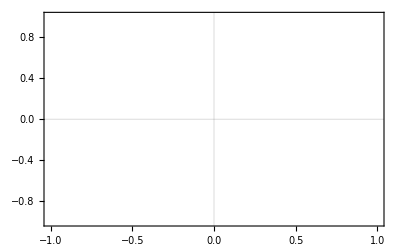

```mathematica
ListPlot[{A01KDl10}]
```

```mathematica
ListPlot[Extrapolation01,PlotRange->All,GridLines->Automatic,FrameLabel->{"K","A_C(K)"},ImageSize->Large]
```

-Graphics-

# Immirzi 1

## Load the Data

```mathematica
SetDirectory[NotebookDirectory[]]
```

/home/pdona/Dropbox/Ongoing Projects/OtherEPRLDivergences/Spinfoam_radiative_corrections/Notebooks

```mathematica
DATA = "../data/EPRL/immirzi_1.0/divergence/cutoff_10.0/frogface_Dl_min_0_Dl_max_10.csv";
```

```mathematica
{rAKDl0,rAKDl1,rAKDl2,rAKDl3,rAKDl4,rAKDl5,rAKDl6,rAKDl7,rAKDl8,rAKDl9,rAKDl10}=Transpose@Import[DATA,"Data",HeaderLines->1];
```

```mathematica
{AKDl0,AKDl1,AKDl2,AKDl3,AKDl4,AKDl5,AKDl6,AKDl7,AKDl8,AKDl9,AKDl10} = Table[{k,#[[2k+1]]},{k,0,10,1/2}]&/@{rAKDl0,rAKDl1,rAKDl2,rAKDl3,rAKDl4,rAKDl5,rAKDl6,rAKDl7,rAKDl8,rAKDl9,rAKDl10};
```

## Extrapolation using Series convergence acceleration

```mathematica
Aitken[AD_]:=(AD[[-1]]AD[[-3]]-AD[[-2]]^2)/(AD[[-1]]-2AD[[-2]]+AD[[-3]])
```

```mathematica
rExtrapolation= Aitken/@Transpose[{rAKDl0,rAKDl1,rAKDl2,rAKDl3,rAKDl4,rAKDl5,rAKDl6,rAKDl7,rAKDl8,rAKDl9,rAKDl10}]
```

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

{Indeterminate,5.22887×10^-14,3.18227×10^-13,4.4819×10^-13,5.3846×10^-13,6.07705×10^-13,6.62165×10^-13,7.06014×10^-13,7.42028×10^-13,7.72103×10^-13,7.97573×10^-13,8.19399×10^-13,8.38292×10^-13,8.5479×10^-13,8.69302×10^-13,8.82152×10^-13,8.93595×10^-13,9.03834×10^-13,9.13038×10^-13,9.21343×10^-13,9.28863×10^-13}

```mathematica
Extrapolationg1=Join[{{0,0}},Table[{k,#[[2k+1]]},{k,1,10,1/2}]&@rExtrapolation]
```

{{0,0},{1,3.18227×10^-13},{3/2,4.4819×10^-13},{2,5.3846×10^-13},{5/2,6.07705×10^-13},{3,6.62165×10^-13},{7/2,7.06014×10^-13},{4,7.42028×10^-13},{9/2,7.72103×10^-13},{5,7.97573×10^-13},{11/2,8.19399×10^-13},{6,8.38292×10^-13},{13/2,8.5479×10^-13},{7,8.69302×10^-13},{15/2,8.82152×10^-13},{8,8.93595×10^-13},{17/2,9.03834×10^-13},{9,9.13038×10^-13},{19/2,9.21343×10^-13},{10,9.28863×10^-13}}

```mathematica
fitExtrapg1=NonlinearModelFit[Extrapolationg1[[5;;]], a Log[k] +b + c/k +d/k^2 ,{a,b,c,d},k]
```

FittedModel[1.00446×10^-12+(9.26324×10^-13)/k^2-(1.419×10^-12)/k+2.49158×10^-14 Log[k]]

```mathematica
fitExtrapg1=NonlinearModelFit[Extrapolationg1[[5;;]], b + c/k +d/k^2 ,{b,c,d},k]
```

FittedModel[1.08251×10^-12+(1.18749×10^-12)/k^2-(1.65993×10^-12)/k]

```mathematica
fitExtrapg1["ParameterConfidenceIntervals"]
```

{{1.08046×10^-12,1.08456×10^-12},{-1.67981×10^-12,-1.64005×10^-12},{1.14594×10^-12,1.22905×10^-12}}

```mathematica
fit1 =First/@fitExtrapg1["ParameterConfidenceIntervals"].{1,1/k , 1/k^2};
fit2 =Last/@fitExtrapg1["ParameterConfidenceIntervals"].{1,1/k , 1/k^2};
```

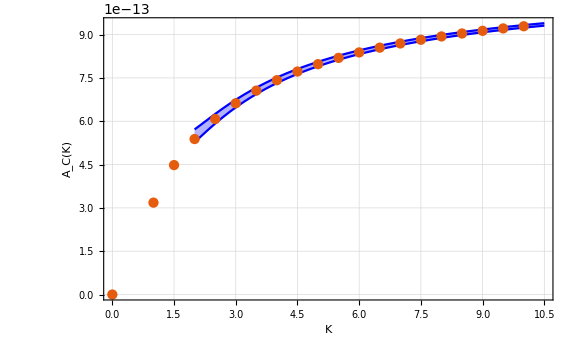

```mathematica
Show[Plot[{fit1,fit2},{k,2,10.5},PlotStyle->Blue,Filling->{1->{2}},GridLines->Automatic,FrameLabel->{"K","A_C(K)"},ImageSize->Large],ListPlot[Extrapolationg1,PlotRange->All],PlotRange->All]
```

# Immirzi 0.1 and dimension (2j+1)^2

## Load the Data

```mathematica
SetDirectory[NotebookDirectory[]]
```

/home/pdona/Dropbox/Ongoing Projects/OtherEPRLDivergences/Spinfoam_radiative_corrections/Notebooks

```mathematica
DATA = "../data/EPRL/immirzi_0.1/divergence/cutoff_10.0/frogface_Dl_min_0_Dl_max_10_dim_2.csv";
```

```mathematica
{rAKDl0,rAKDl1,rAKDl2,rAKDl3,rAKDl4,rAKDl5,rAKDl6,rAKDl7,rAKDl8,rAKDl9,rAKDl10}=Transpose@Import[DATA,"Data",HeaderLines->1];
```

```mathematica
{AKDl0,AKDl1,AKDl2,AKDl3,AKDl4,AKDl5,AKDl6,AKDl7,AKDl8,AKDl9,AKDl10} = Table[{k,#[[2k+1]]},{k,0,10,1/2}]&/@{rAKDl0,rAKDl1,rAKDl2,rAKDl3,rAKDl4,rAKDl5,rAKDl6,rAKDl7,rAKDl8,rAKDl9,rAKDl10};
```

## Extrapolation using Series convergence acceleration

```mathematica
Aitken[AD_]:=(AD[[-1]]AD[[-3]]-AD[[-2]]^2)/(AD[[-1]]-2AD[[-2]]+AD[[-3]])
```

```mathematica
rExtrapolation= Aitken/@Transpose[{rAKDl0,rAKDl1,rAKDl2,rAKDl3,rAKDl4,rAKDl5,rAKDl6,rAKDl7,rAKDl8,rAKDl9,rAKDl10}]
```

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

{Indeterminate,1.49902×10^-7,1.83178×10^-6,3.73993×10^-6,5.67121×10^-6,7.8159×10^-6,0.0000101895,0.0000127974,0.0000156418,0.000018724,0.0000220455,0.0000256082,0.0000294152,0.0000334703,0.0000377783,0.0000423452,0.0000471774,0.0000522825,0.0000576686,0.0000633447,0.0000693208}

```mathematica
Extrapolation=Join[{{0,0}},Table[{k,#[[2k+1]]},{k,1/2,10,1/2}]&@rExtrapolation]
```

{{0,0},{1/2,1.49902×10^-7},{1,1.83178×10^-6},{3/2,3.73993×10^-6},{2,5.67121×10^-6},{5/2,7.8159×10^-6},{3,0.0000101895},{7/2,0.0000127974},{4,0.0000156418},{9/2,0.000018724},{5,0.0000220455},{11/2,0.0000256082},{6,0.0000294152},{13/2,0.0000334703},{7,0.0000377783},{15/2,0.0000423452},{8,0.0000471774},{17/2,0.0000522825},{9,0.0000576686},{19/2,0.0000633447},{10,0.0000693208}}

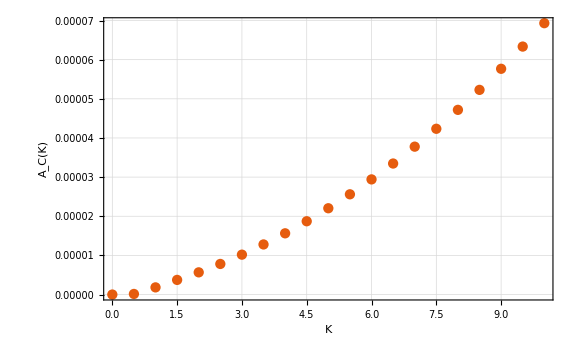

```mathematica
ListPlot[Extrapolation,PlotRange->All,GridLines->Automatic,FrameLabel->{"K","A_C(K)"},ImageSize->Large]
```

```mathematica
fitExtrap=NonlinearModelFit[Extrapolation[[5;;]],a k^3+ b k^2 + c k+ d,{a,b,c,d},k]
```

FittedModel[-8.84847×10^-7+2.45239×10^-6 k+3.96413×10^-7 k^2+6.01962×10^-9 k^3]

```mathematica
(Normal[fitExtrap]/.Plus->List)/.k->10
```

{-8.84847×10^-7,0.0000245239,0.0000396413,6.01962×10^-6}

```mathematica
fitExtrap["BestFitParameters"]
```

{a→6.01962×10^-9,b→3.96413×10^-7,c→2.45239×10^-6,d→-8.84847×10^-7}